# Simulation of my hypothesis for the online-exp

## Model

q[i][t]=(1-λ) softmax+λ conformity[n,θ]

whose softmax parameters (learning rate & temperature) are optimize for asocial condition. Varying λ and θ, I aim to check whether tradeoff between noise reduction benefit and herding effect would emerge.

## Intermediate condition

Round[RandomVariate[NormalDistribution[3.1-2*0.742,0.55],1],0.1](*low*)
Round[RandomVariate[NormalDistribution[3.1-0.642,0.55],1],0.1](*mid*)
Round[RandomVariate[NormalDistribution[3.1,0.55],1],0.1](*high*)

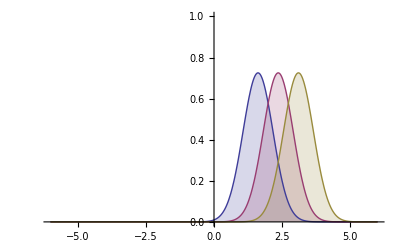

```mathematica
Plot[Evaluate@Table[PDF[NormalDistribution[μ,0.55],x],{μ,{3.1-2*0.742,3.1-0.742,3.1}}],{x,-6,6},Filling->Axis,PlotRange->{0,1}]
```

### Parameter setting: lifetime = 70, changing at 41 (1-40: environment 1, 41-70: environment 2)

Note that both LR and Temp parameters are drawn from normal distributions whose means and SDs are based on the experimental result

```mathematica
(* -- settings -- *)
lifetime=70;
changingPoint=41;
replication=10000;(*10000*)

basePayoffMean=3.1;
payoffSD=0.55;
qualityDiff=0.742;
boxDistribution1={0,0,1};
boxDistribution2={2,0,1};

groupSizes={3,10,30};
Lambda=Flatten[{0.01,Table[i,{i,0.1,0.9,0.1}]}];
Theta={0.5,1,3,6};

(* param means and sds *)
alphaRawMuGroup=0.90;
alphaRawSDGroup=1.61;
(*betaMuGroup=3.17;
betaSDGroup=1.09;*)
betaMean=1.68;
annealingMean=3.01;
betaSd=0.64;
annealingSd=2.04;
alphaRawMuIndiv=-0.05;
alphaRawSDIndiv=2.14;
betaMuIndiv=2.7;
betaSDIndiv=1.13;
thetaSD=2.69;
lambdaSD=2;


(* ---- *)
lengthBoxDistribution=Length[boxDistribution1];
inherentExpect=1.*^-10;
boxMeans1=Table[basePayoffMean,{lengthBoxDistribution}]+boxDistribution1*qualityDiff;
boxMeans2=Table[basePayoffMean,{lengthBoxDistribution}]+boxDistribution2*qualityDiff;
payoffGenerate[m_]:=Round[RandomVariate[NormalDistribution[m,payoffSD],1],0.01];
```

### Simulation:

```mathematica
LandscapeSimulation=
ParallelTable[
{n,
θ,
λ,

Machine={};
Perform={};
OptimalChoiceRate={};
Mergeperform={};
AverageQ={};
MergeOptimalChoiceRate={};
GroupTotalPerform={};
GroupAverageOptimalChoiceRateFirstHalf={};
GroupAverageOptimalChoiceRateSecondHalf={};

Do[{
(*initialization*)
choiceCount=Table[0,{n},{lengthBoxDistribution}];
totalEarning=Table[0,{n},{lengthBoxDistribution}];
Q=Table[inherentExpect,{n},{lengthBoxDistribution}];
socialFrequency=Table[0.1,{lifetime},{lengthBoxDistribution}];
If[n>1,
alphaRaw=alphaRawMuGroup+alphaRawSDGroup*RandomVariate[StudentTDistribution[0,1,14],n],
alphaRaw=alphaRawMuIndiv+alphaRawSDIndiv*RandomVariate[StudentTDistribution[0,1,14],n]
];
alpha=1/(1+Exp[-alphaRaw]);
If[n>1,
beta=betaMean+betaSd*RandomVariate[StudentTDistribution[0,1,14],n],
beta=betaMean+betaSd*RandomVariate[StudentTDistribution[0,1,14],n]
];
(*beta= ReplacePart[beta0,Position[beta0,n_ /; n<0]->0];*)
annealing=annealingMean+annealingSd*RandomVariate[StudentTDistribution[0,1,14],n];
thisInvTemp=Exp[beta+(1/70)*annealing];
theta=θ+thetaSD*RandomVariate[StudentTDistribution[0,1,14],n];
lambdaRaw=Log[λ/(1-λ)]+lambdaSD*RandomVariate[StudentTDistribution[0,1,14],n];
If[n>1,
lambda=1/(1+Exp[-lambdaRaw]),
lambda=0
];
(*If[Length[Position[lambda,_?Negative]]>0,
lambda=ReplacePart[lambda,Position[lambda,_?Negative][[1]]->0]
];*)
e=E^(thisInvTemp Q);
machine={};
perform={};
optimal={};
mergeoptimal={};
mergeperform={};
averageq={};
payoffHistory=Table[0,{n},{lifetime}];

(*群れの１試行*)
Do[{
periMachine={};
periPerform={};
periMeanQ={};
periOptimal={};
thisInvTemp=Exp[beta+(t/70)*annealing];


(*n-players select one machine simultaneously*)
Do[{
(*random choice*)
SeedRandom[10+(r^2)*(t^2+i^3)];
k=RandomChoice[e[[i]]->Table[b,{b,lengthBoxDistribution}]];
(*get payoff from machine-k*)
SeedRandom[1001+(r^2)*(t^3+i^2)];
If[t<changingPoint,
payoff=payoffGenerate[boxMeans1[[k]]][[1]];,
payoff=payoffGenerate[boxMeans2[[k]]][[1]];
];
If[payoff<0.,payoff=0.0];
If[t<changingPoint,
performance=boxDistribution1[[k]];,
performance=boxDistribution2[[k]];
];
If[t<changingPoint,
If[boxDistribution1[[k]]==1,optimalCounter=1;,optimalCounter=0;];,
If[boxDistribution2[[k]]==2,optimalCounter=1;,optimalCounter=0;];
];
(*update the list "count"*)
choiceCount=ReplacePart[choiceCount,{i,k}->choiceCount[[i]][[k]]+1];
(*update the list "total"*)
totalEarning=ReplacePart[totalEarning,{i,k}->totalEarning[[i]][[k]]+payoff];
(*update the social frequency*)
socialFrequency=ReplacePart[socialFrequency,{t,k}->socialFrequency[[t]][[k]]+1];

(*counting each player's machine in this period*)
periMachine=Append[periMachine,k],
(*counting each player's performance in this period*)
periPerform=Append[periPerform,performance],
periOptimal=Append[periOptimal,optimalCounter],

payoffHistory=ReplacePart[payoffHistory,{i,t}->payoff];

(*update the list "Q" of individual i *)
If[t==1,
{
Q=ReplacePart[Q,{i,1}->(1-alpha[[i]])*Q[[i]][[1]]+alpha[[i]]*payoff],
Q=ReplacePart[Q,{i,2}->(1-alpha[[i]])*Q[[i]][[2]]+alpha[[i]]*payoff],
Q=ReplacePart[Q,{i,3}->(1-alpha[[i]])*Q[[i]][[3]]+alpha[[i]]*payoff]
};,
Q=ReplacePart[Q,{i,k}->(1-alpha[[i]])*Q[[i]][[k]]+alpha[[i]]*payoff];
]


},{i,1,n}];


(*updating of the list "e"*)
(*shannon's entropy*)
(*SHANNON=
Table[
Total[-{E^(beta Q)/Total[E^(beta Q),{2}]}[[1]][[i]]*Log[lengthBoxDistribution,{E^(beta Q)/Total[E^(beta Q),{2}]}[[1]][[i]]]]
,{i,1,Length[Q]}
];*)
social=Table[0,{n}];
Do[{social[[i]]=socialFrequency[[t]]^theta[[i]]/Total[socialFrequency[[t]]^theta[[i]]]},{i,1,n}];
e=(1.0-lambda)*E^(thisInvTemp Q)/Total[E^(thisInvTemp Q),{2}]+lambda*social;
(*e=(1.0-lambda)*E^(beta Q)/Total[E^(beta Q),{2}]+lambda*Table[socialFrequency[[t]]^theta/Total[socialFrequency[[t]]^theta],{n}];*)
(*e=(1-SHANNON)*E^(beta Q)/Total[E^(beta Q),{2}]+SHANNON*Table[socialFrequency[[t]]^θ/Total[socialFrequency[[t]]^θ],{n}];*)


(*adding to the List "machine"*)
machine=Append[machine,periMachine],

(*raw performance*)
perform=Append[perform,periPerform],
optimal=Append[optimal,periOptimal],

averageq=Append[averageq,Mean[Q]],

(*mergeperformance*)
mergeperform=Append[mergeperform,Mean[periPerform]],
mergeoptimal=Append[mergeoptimal,Mean[periOptimal]]

},{t,1,lifetime}];

Machine=Append[Machine,{machine}],
Perform=Append[Perform,{perform}],
OptimalChoiceRate=Append[OptimalChoiceRate,{optimal}],
AverageQ=Append[AverageQ,{averageq}],
Mergeperform=Append[Mergeperform,{mergeperform}],
MergeOptimalChoiceRate=Append[MergeOptimalChoiceRate,{mergeoptimal}],
GroupTotalPerform=Append[GroupTotalPerform, Total[mergeperform]],
GroupAverageOptimalChoiceRateFirstHalf=Append[GroupAverageOptimalChoiceRateFirstHalf,Mean[mergeoptimal[[1;;(changingPoint-1)]]]],
GroupAverageOptimalChoiceRateSecondHalf=Append[GroupAverageOptimalChoiceRateSecondHalf,Mean[mergeoptimal[[changingPoint;;lifetime]]]]

},{r,replication}];

(*累積成績の計算*)
timeseriesOptimalRate=Total[MergeOptimalChoiceRate]/replication,
Mean[timeseriesOptimalRate[[1]]],
GroupTotalPerform,
GroupAverageOptimalChoiceRateFirstHalf,
GroupAverageOptimalChoiceRateSecondHalf
}

,{λ,Lambda},{θ,Theta},{n,groupSizes}];

LandscapeSimulation2=LandscapeSimulation;
LandscapeSimulation2=Partition[Flatten[LandscapeSimulation2],lifetime+(replication*3)+4];
names=Join[{"groupSize","theta","lambda"},
Table["t"<>ToString[t],{t,1,lifetime}],
{"totalPerformance"},
Table["total_g"<>ToString[g],{g,1,replication}],
Table["firstHalf_g"<>ToString[g],{g,1,replication}],
Table["secondHalf_g"<>ToString[g],{g,1,replication}]
];
LandscapeSimulation2=Insert[LandscapeSimulation2,names,1];
(*ディレクトリを指定*)
SetDirectory[NotebookDirectory[]];
(*シミュレーション結果をCSVファイルとして保存する*)
Export["simulationResults/UNC_Moderate_expParameters_timeSeries.csv",N[LandscapeSimulation2[[All,1;;lifetime+3]]]]

LandscapeSimulation3=LandscapeSimulation;
LandscapeSimulation3=Partition[Flatten[LandscapeSimulation3],lifetime+(replication*3)+4];
totalPerformanceEachGroup=Partition[Flatten[N[LandscapeSimulation3[[All,4+1+lifetime;;4+lifetime+replication]]]],1];
AverageOptimEachGroupFirstHalf=Partition[Flatten[N[LandscapeSimulation3[[All,4+lifetime+replication+1;;4+lifetime+(2*replication)]]]],1];
AverageOptimEachGroupSecondHalf=Partition[Flatten[N[LandscapeSimulation3[[All,4+lifetime+2*replication+1;;4+lifetime+(3*replication)]]]],1];
LandscapeSimulation3=Join[Join[Join[Partition[Flatten[Table[{n,θ,λ,i},{λ,Lambda},{θ,Theta},{n,groupSizes},{i,replication}]],4],totalPerformanceEachGroup,2],AverageOptimEachGroupFirstHalf,2],AverageOptimEachGroupSecondHalf,2];
names2={"groupSize","theta","lambda","replication","totalPerform","averageFirst","averageSecond"};
LandscapeSimulation3=Insert[LandscapeSimulation3,names2,1];
(*ディレクトリを指定*)
SetDirectory[NotebookDirectory[]];
(*シミュレーション結果をCSVファイルとして保存する*)
Export["simulationResults/UNC_Moderate_expParameters_eachGroup.csv",N[LandscapeSimulation3]]
```

simulationResults/UNC_Moderate_expParameters_timeSeries.csv

simulationResults/UNC_Moderate_expParameters_eachGroup.csv

### Plot optimal choice rate:

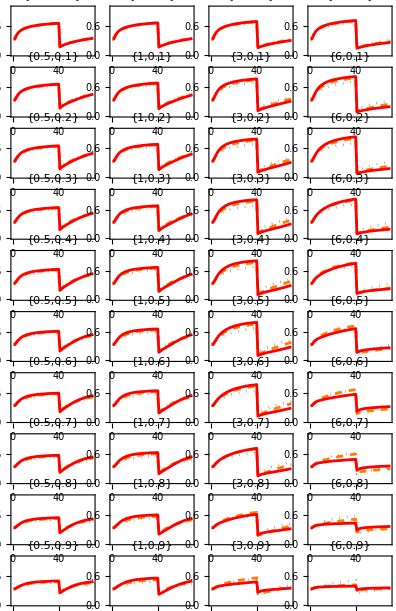

figure001.pdf

```mathematica
fig1=Show[GraphicsGrid[Table[
ListLinePlot[
Table[
Take[LandscapeSimulation2[[
Position[Transpose[{Transpose[N[LandscapeSimulation2]][[2]],Transpose[N[LandscapeSimulation2]][[3]]}],{N[θ],N[λ]}][[i]]
]][[1]],{4,lifetime+3}]
,{i,1,Length[groupSizes]}]
,Frame->True,PlotRange->{0,1},PlotLabel->{θ,λ},LabelStyle->{12,FontFamily->"Times New Roman"},
PlotStyle->Transpose[{Append[Append[Table[GrayLevel[.8-0.2*i],{i,1,Length[groupSizes]-2}],Orange],Red],{Dotted,Dashed,Bold},{AbsoluteThickness[2],AbsoluteThickness[2],AbsoluteThickness[2]}}]]
,{λ,Lambda},{θ,Theta}]
,Spacings->{Scaled[0],Scaled[0]}],
ImageSize->140*72/25.4,AxesLabel->{"Round","Choice accuracy"}
]
(*Table[
Histogram[
Table[
Take[LandscapeSimulation2[[
Position[Transpose[{Transpose[N[LandscapeSimulation2]][[2]],Transpose[N[LandscapeSimulation2]][[3]]}],{N[θ],N[λ]}][[i]]
]][[1]],{lifetime+5,lifetime+replication+4}]
,{i,1,Length[groupSizes]}]
,PlotRange->{0,2},PlotLabel->{θ,λ}]
,{λ,lambda},{θ,theta}]*)
Export["figure001.pdf",fig1]
```

## Weak conformity vs strong conformity

```mathematica
(* -- settings -- *)
lifetime=70;
changingPoint=41;
replication=1000;(*10000*)

basePayoffMean=3.1;
payoffSD=0.55;
qualityDiff=0.742;
boxDistribution1={0,0,1};
boxDistribution2={2,0,1};

groupSizes={5,10,15};
Lambda={0.2,0.7};
Theta={1,3};
(*alphaRawMuGroup=0.84;
alphaRawSDGroup=1.48;
betaMuGroup=3.17;
betaSDGroup=1.09;
alphaRawMuIndiv=-0.05;
alphaRawSDIndiv=2.14;
betaMuIndiv=2.7;
betaSDIndiv=1.13;
thetaSD=0.5;
lambdaSD=1;*)


(* ---- *)
lengthBoxDistribution=Length[boxDistribution1];
inherentExpect=1.*^-10;
boxMeans1=Table[basePayoffMean,{lengthBoxDistribution}]+boxDistribution1*qualityDiff;
boxMeans2=Table[basePayoffMean,{lengthBoxDistribution}]+boxDistribution2*qualityDiff;
payoffGenerate[m_]:=Round[RandomVariate[NormalDistribution[m,payoffSD],1],0.1];
```

### Simulation:

```mathematica
LandscapeSimulationTimeSeries=
ParallelTable[
{n,
θ,
λ,

Machine={};
Perform={};
OptimalChoiceRate={};
Mergeperform={};
AverageQ={};
MergeOptimalChoiceRate={};
GroupTotalPerform={};
GroupAverageOptimalChoiceRateFirstHalf={};
GroupAverageOptimalChoiceRateSecondHalf={};

Do[{
(*initialization*)
choiceCount=Table[0,{n},{lengthBoxDistribution}];
totalEarning=Table[0,{n},{lengthBoxDistribution}];
Q=Table[inherentExpect,{n},{lengthBoxDistribution}];
socialFrequency=Table[0.1,{lifetime},{lengthBoxDistribution}];
If[n>1,
alphaRaw=RandomVariate[NormalDistribution[alphaRawMuGroup,alphaRawSDGroup],n],
alphaRaw=RandomVariate[NormalDistribution[alphaRawMuIndiv,alphaRawSDIndiv],n]
];
alpha=1/(1+Exp[-alphaRaw]);
If[n>1,
beta=RandomVariate[NormalDistribution[betaMuGroup,betaSDGroup],n],
beta=RandomVariate[NormalDistribution[betaMuGroup,betaSDGroup],n]
];
theta=θ+RandomVariate[NormalDistribution[0,thetaSD],n];
lambdaRaw=Log[λ/(1-λ)]+RandomVariate[NormalDistribution[0,lambdaSD],n];
If[n>1,
lambda=1/(1+Exp[-lambdaRaw]),
lambda=0
];
(*If[Length[Position[lambda,_?Negative]]>0,
lambda=ReplacePart[lambda,Position[lambda,_?Negative][[1]]->0]
];*)
e=E^(beta Q);
machine={};
perform={};
optimal={};
mergeoptimal={};
mergeperform={};
averageq={};
payoffHistory=Table[0,{n},{lifetime}];

(*群れの１試行*)
Do[{
periMachine={};
periPerform={};
periMeanQ={};
periOptimal={};


(*n-players select one machine simultaneously*)
Do[{
(*random choice*)
SeedRandom[10+(r^2)*(t^2+i^3)];
k=RandomChoice[e[[i]]->Table[b,{b,lengthBoxDistribution}]];
(*get payoff from machine-k*)
SeedRandom[1001+(r^2)*(t^3+i^2)];
If[t<changingPoint,
payoff=payoffGenerate[boxMeans1[[k]]][[1]];,
payoff=payoffGenerate[boxMeans2[[k]]][[1]];
];
If[payoff<0.,payoff=0.0];
If[t<changingPoint,
performance=boxDistribution1[[k]];,
performance=boxDistribution2[[k]];
];
If[t<changingPoint,
If[boxDistribution1[[k]]==1,optimalCounter=1;,optimalCounter=0;];,
If[boxDistribution2[[k]]==2,optimalCounter=1;,optimalCounter=0;];
];
(*update the list "count"*)
choiceCount=ReplacePart[choiceCount,{i,k}->choiceCount[[i]][[k]]+1];
(*update the list "total"*)
totalEarning=ReplacePart[totalEarning,{i,k}->totalEarning[[i]][[k]]+payoff];
(*update the social frequency*)
socialFrequency=ReplacePart[socialFrequency,{t,k}->socialFrequency[[t]][[k]]+1];

(*counting each player's machine in this period*)
periMachine=Append[periMachine,k],
(*counting each player's performance in this period*)
periPerform=Append[periPerform,performance],
periOptimal=Append[periOptimal,optimalCounter],

payoffHistory=ReplacePart[payoffHistory,{i,t}->payoff];

(*update the list "Q" of individual i *)
Q=ReplacePart[Q,{i,k}->(1-alpha[[i]])*Q[[i]][[k]]+alpha[[i]]*payoff]

},{i,1,n}];


(*updating of the list "e"*)
(*shannon's entropy*)
(*SHANNON=
Table[
Total[-{E^(beta Q)/Total[E^(beta Q),{2}]}[[1]][[i]]*Log[lengthBoxDistribution,{E^(beta Q)/Total[E^(beta Q),{2}]}[[1]][[i]]]]
,{i,1,Length[Q]}
];*)
social=Table[0,{n}];
Do[{social[[i]]=socialFrequency[[t]]^theta[[i]]/Total[socialFrequency[[t]]^theta[[i]]]},{i,1,n}];
e=(1.0-lambda)*E^(beta Q)/Total[E^(beta Q),{2}]+lambda*social;
(*e=(1.0-lambda)*E^(beta Q)/Total[E^(beta Q),{2}]+lambda*Table[socialFrequency[[t]]^theta/Total[socialFrequency[[t]]^theta],{n}];*)
(*e=(1-SHANNON)*E^(beta Q)/Total[E^(beta Q),{2}]+SHANNON*Table[socialFrequency[[t]]^θ/Total[socialFrequency[[t]]^θ],{n}];*)


(*adding to the List "machine"*)
machine=Append[machine,periMachine],

(*raw performance*)
perform=Append[perform,periPerform],
optimal=Append[optimal,periOptimal],

averageq=Append[averageq,Mean[Q]],

(*mergeperformance*)
mergeperform=Append[mergeperform,Mean[periPerform]],
mergeoptimal=Append[mergeoptimal,Mean[periOptimal]]

},{t,1,lifetime}];

Machine=Append[Machine,{machine}],
Perform=Append[Perform,{perform}],
OptimalChoiceRate=Append[OptimalChoiceRate,{optimal}],
AverageQ=Append[AverageQ,{averageq}],
Mergeperform=Append[Mergeperform,{mergeperform}],
MergeOptimalChoiceRate=Append[MergeOptimalChoiceRate,{mergeoptimal}](*,
GroupTotalPerform=Append[GroupTotalPerform, Total[mergeperform]],
GroupAverageOptimalChoiceRateFirstHalf=Append[GroupAverageOptimalChoiceRateFirstHalf,Mean[mergeoptimal[[1;;(changingPoint-1)]]]],
GroupAverageOptimalChoiceRateSecondHalf=Append[GroupAverageOptimalChoiceRateSecondHalf,Mean[mergeoptimal[[changingPoint;;lifetime]]]]*)

},{r,replication}];

(*累積成績の計算*)
(*timeseriesOptimalRate=Total[MergeOptimalChoiceRate]/replication,
Mean[timeseriesOptimalRate[[1]]],*)
(*GroupTotalPerform,*)
MergeOptimalChoiceRate
(*GroupAverageOptimalChoiceRateFirstHalf,
GroupAverageOptimalChoiceRateSecondHalf*)
}

,{λ,Lambda},{θ,Theta},{n,groupSizes}];


LandscapeSimulation4=LandscapeSimulationTimeSeries;
LandscapeSimulation4=Partition[Flatten[LandscapeSimulation4],lifetime*replication+3];
LandscapeSimulation4=Partition[Flatten[Drop[LandscapeSimulation4,None,3]],1];
LandscapeSimulation4=Join[{{"groupSize","theta","lambda","replication","round","optimalChoiceRate"}},Join[Partition[Flatten[Table[{n,θ,λ,i,t},{λ,Lambda},{θ,Theta},{n,groupSizes},{i,replication},{t,lifetime}]],5],LandscapeSimulation4,2],1];
(*ディレクトリを指定*)
SetDirectory[NotebookDirectory[]];
(*シミュレーション結果をCSVファイルとして保存する*)
Export["simulationResults/UNC_Moderate_expParameters_timeSeriesEachGroup.csv",N[LandscapeSimulation4]]
```

simulationResults/UNC_Moderate_expParameters_timeSeriesEachGroup.csv